# Aggressive Early Deflation

Working through Braman, Byers and Mathias. SIMA JMat Analysis 2002 MultiShift Part 2

## Opening Example

```mathematica
m=6;
A=SparseArray[ {
Band[{1,1}]->{6,1,2,3,4,5},
Band[{1,1},{1,m},{0,1}]->{6,5,4,3,2,1},
Band[{2,1}]->0.001},
{m,m}];
MatrixForm[A]
Dia={6,5,4,3,2,1};
TableForm[{λ=Eigenvalues[A],Abs[λ-Dia]/Dia}ᵀ]
```

(6 | 5 | 4 | 3 | 2 | 1
0.001 | 1 | 0 | 0 | 0 | 0
0 | 0.001 | 2 | 0 | 0 | 0
0 | 0 | 0.001 | 3 | 0 | 0
0 | 0 | 0 | 0.001 | 4 | 0
0 | 0 | 0 | 0 | 0.001 | 5)

6.001 | 0.000166667
5. | 1.77636×10^-16
4. | 4.11893×10^-14
3. | 1.66416×10^-10
2. | 4.99002×10^-7
0.999001 | 0.000999001

## Hessenberg Plus Spike Discussion “Bottom” p950

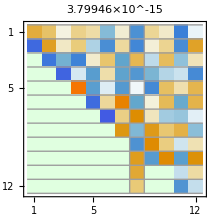
I can “Schur” the bottom k×k block of a Hessenberg matrix.  It makes a vertical spike. 
	Ĥ=-Graphics-
The spike is in the -(k+1)=n-k-1 column.  I am going to think of the spike as rooted in the on the diagonal. With this understanding the spike is Ĥ⟦-(k+1);;-1, -(k+1)⟧. The observation from the paper is that the bottom entries of this spike can be tiny even if the original Hessenberg form is not nearly reducible by traditional standards.  Schur decomposition seems to naturally grade the spike so that small entries are near the bottom.  As long as the lower block is reasonably sized the “real” schur form does not seem to cause many issues.

#### Demo

```mathematica
{n,k}={12,4};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H33=H⟦-k;;-1,-k;;-1⟧;
{Q,T}=SchurDecomposition[H33];
QBig=IdentityMatrix[n]; QBig⟦-k;;-1,-k;;-1⟧=Q;
QBtHQB=Chop[QBigᵀ.H.QBig];
TabView[{
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[QBtHQB,PlotLabel->Norm[H33-Q.T.Qᵀ],
ColorRules->{0->LightGreen},
Mesh->{All,{n-k-1,n-k}}],
"V-Spike"->ListPlot[QBtHQB⟦All,n-k⟧],
"H"->MatrixPlot[Chop[H]]
}]
```

123

## Hessenberg Plus Spike Discussion Top

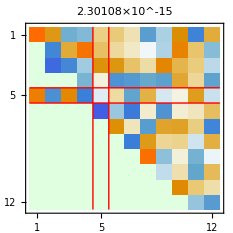
I can “Schur” the top k×k block of a Hessenberg matrix.  It makes a horizontal spike. 
	Ĥ=-Graphics-
The spike is in row k+1 .  I am going to think of the spike as rooted on the diagonal. With this understanding the spike is Ĥ⟦k+1, 1;;k+1⟧. Just like the column spikes the last entries of this spike can be tiny even if the original Hessenberg form is not nearly reducible by traditional standards.  Schur decomposition seems to naturally grade the spike so that small entries are near the bottom.  As long as the selected block is reasonably sized the “real” schur form does not seem to cause many issues.

#### Demo

```mathematica
{n,k}={32,9};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H11=H⟦1;;k,1;;k⟧;
{Q,T}=SchurDecomposition[H11];
QBig=IdentityMatrix[n]; QBig⟦1;;k,1;;k⟧=Q;
QBtHQB=Chop[QBigᵀ.H.QBig];
Spike=0*H; Spike⟦{k+1},1;;k+1⟧=QBtHQB⟦{k+1},1;;k+1⟧;
TabView[{
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[QBtHQB,PlotLabel->Norm[H11-Q.T.Qᵀ],
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1},{k,k+1}}],
"H-Spike"->MatrixPlot[Spike, PlotLegends->Automatic,MeshStyle->Red,
Mesh->{{k,k+1},{k,k+1}}],
"H"->MatrixPlot[Chop[H]]
}]
```

123

## Hessenberg Plus Double Spike Discussion

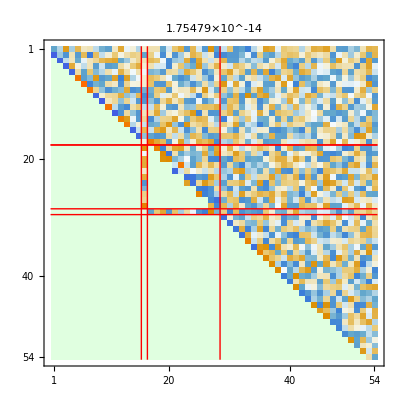
If do the same process in the middle we get two spikes that frame a central Schur form.  I am going to describe this with an m_1 for the start of a k×k Schur decomposition.  The spikes “frame” the reduced block
	Ĥ=-Graphics-

### Demo

```mathematica
{n,m1,k}={54,17,11};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H22=H⟦m1;;m1+k,m1;;m1+k⟧;
{Q,T}=SchurDecomposition[H22];
QBig=IdentityMatrix[n]; QBig⟦m1;;m1+k,m1;;m1+k⟧=Q;
QBtHQB=QBigᵀ.H.QBig;
MatrixPlot[Chop[QBtHQB],PlotLabel->Norm[H22-Q.T.Qᵀ],ColorRules->{0->LightGreen},
MeshStyle->Red,
Mesh->{{m1,m1,m1+k,m1+k+1},{m1-2,m1-1,m1+k}}]
```

-Graphics-

```mathematica
TabView[{
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[
Chop[QBtHQB],PlotLabel->Norm[H22-Q.T.Qᵀ],ColorRules->{0->LightGreen},
MeshStyle->Red,
Mesh->{{m1,m1,m1+k,m1+k+1},{m1-2,m1-1,m1+k}}],
"V and H Spikes"->ListPlot[
{QBtHQB⟦All,n1⟧,QBtHQB⟦n2+1,All⟧},
PlotRange->All,Joined->True,Mesh->All],
"H"->MatrixPlot[Chop[H]]
}]
```

123

## Spike Form ⟺ Hessenberg Form

The paper discusses Spike ⇒Hessenberg.  There has to be a natural way to go the other way. The simple “high-level” way to think about this is as just doing a Hessenberg on the spiked form. I think this is a strict inverse operation with a sign definite QR and Hessenberg.   I am going to do this on the top version first.

OK there are two things I do not understand here!

#### Demo

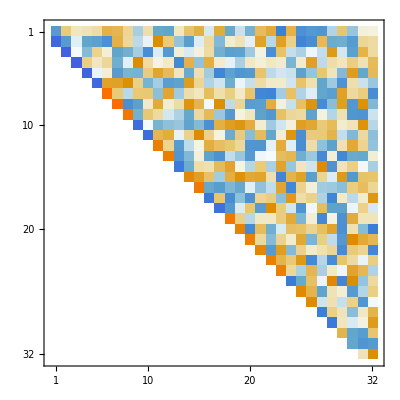
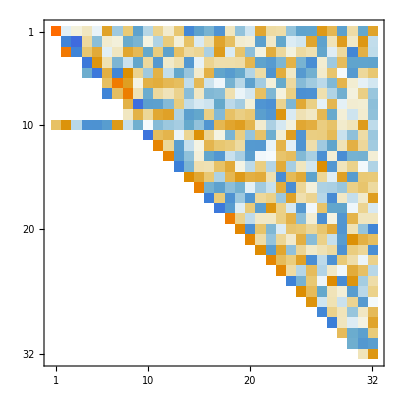
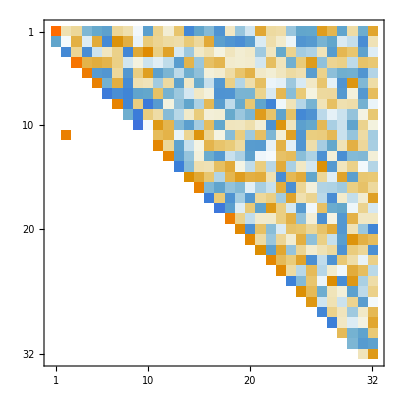

```mathematica
{n,k}={32,9};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H11=H⟦1;;k,1;;k⟧;
{Q,T}=SchurDecomposition[H11];
QBig=IdentityMatrix[n]; QBig⟦1;;k,1;;k⟧=Q;
QBtHQB=Chop[QBigᵀ.H.QBig];
{QBack,HBack}=HessenbergDecomposition[QBtHQB⟦1;;k+1,1;;k+1⟧];
QBackBig=IdentityMatrix[n]; QBackBig⟦1;;k+1,1;;k+1⟧=QBackᵀ;
HBackBig=Chop[QBackBig.QBtHQB.QBackBigᵀ];
Spike=0*H; Spike⟦{k+1},1;;k+1⟧=QBtHQB⟦{k+1},1;;k+1⟧;
TabView[{
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[QBtHQB,PlotLabel->Norm[H11-Q.T.Qᵀ],
ColorRules->{0->LightGreen},MeshStyle->Red,
Mesh->{{k,k+1},{k,k+1}}],
"H-Spike"->MatrixPlot[Spike, PlotLegends->Automatic,MeshStyle->Red,
Mesh->{{k,k+1},{k,k+1}}],
"H"->MatrixPlot[Chop[H]]
}];
Map[MatrixPlot,{H, QBtHQB, HBackBig}]
```

```mathematica
{n,n1,n2}={54,11,23};
H=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]]⟦2⟧;
H22=H⟦n1+1;;n2,n1+1;;n2⟧;
{Q,T}=SchurDecomposition[H22];
QBig=IdentityMatrix[n]; QBig⟦n1+1;;n2,n1+1;;n2⟧=Q;
QBtHQB=QBigᵀ.H.QBig;
TabView[{
"H"->MatrixPlot[Chop[H]],
"Q_Bigᵀ.H.Q_Big"->MatrixPlot[Chop[QBtHQB],PlotLabel->Norm[H22-Q.T.Qᵀ],ColorRules->{0->LightGreen},
Mesh->{{n1,n2},{n1,n2}}],
"V and H Spikes"->ListPlot[
{QBtHQB⟦All,n1⟧,QBtHQB⟦n2+1,All⟧},
GridLines->{{n1,n2},None},PlotRange->All,Joined->True,Mesh->All]
}]
```

123

```mathematica
m=6;
A=SparseArray[ {
Band[{1,1}]->{6,1,2,3,4,5},
Band[{1,1},{1,m},{0,1}]->{6,5,4,3,2,1},
Band[{2,1}]->0.001},
{m,m}];
Dia={6,5,4,3,2,1};
Abs[Eigenvalues[A]-Dia]/Dia
```

{0.000166667,1.77636×10^-16,4.11893×10^-14,1.66416×10^-10,4.99002×10^-7,0.000999001}

## Break

I have an m×n QRDecomomp A=Q.R and I want to add a block of s columns and compute an expanded QRDecomoposition [A|Ã]=Q̃.R̃.

I have an (m+s)×n QRDecomomp [A|Ã]=Q̃.R̃ and I want to delete a block of s columns and compute a smaller QRDecomoposition A=Q.R.

What I really want to do is replace a block of “s” columns in the decomposition.  I think this is just a low rank-update

```mathematica
{m,n}={12,7};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRDecomposition[A];Q=Qᵀ;
k=3;
a=A⟦All,k⟧;
Dimensions[a];
B=A+KroneckerProduct[(SparseArray[k->1,m]-a),SparseArray[k->1,n]] ;
Map[Dimensions,{Qᵀ,B}]
MatrixForm[Chop[Qᵀ.B]]
```

{{7,12},{12,7}}

(-2.36778 | 0.314716 | 0.330718 | 1.1291 | -0.201299 | 0.676782 | -0.458518
0 | -1.69737 | 0.0896672 | -0.15501 | 0.331842 | -0.104867 | -0.966413
0 | 0 | -0.156154 | -0.818367 | -0.872829 | 0.769191 | 1.12149
0 | 0 | 0.310656 | -1.22816 | 0.256325 | 0.0299952 | -0.608911
0 | 0 | 0.266002 | 0 | 1.71747 | 0.567402 | 0.76841
0 | 0 | -0.136583 | 0 | 0 | -1.5919 | -0.0942493
0 | 0 | -0.316617 | 0 | 0 | 0 | 1.57966)

## C